```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/fluctuations_T

## Data

### QM model Nf=2

```mathematica
TcQM=184;
V=Flatten[Import["./PQM2flavor/buffer/Vtotal.dat"]]*197.33^4;
T=Flatten[Import["./PQM2flavor/buffer/TMeV.dat"]];
p=Transpose[{T/TcQM,-(V-V[[1]])/T^4}];
pTdata=Transpose[{T,-(V-V[[1]])}];
Intp=Interpolation[pTdata];
dpdT[x_]=D[Intp[x],x];
dpdT2[x_]=D[Intp[x],{x,2}];
csNf2=Transpose[{T/TcQM,dpdT[T]/(T*dpdT2[T])}];
(*Show[ListLinePlot[pTdata],Plot[Intp[x],{x,2,500},PlotStyle->{Dashed,Red}]]*)
```

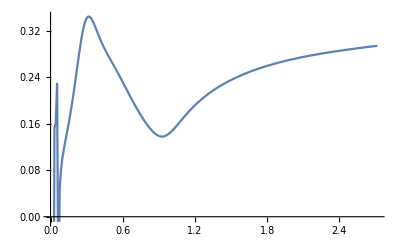

```mathematica
ListLinePlot[csNf2]
```

### QM model Nf=2+1

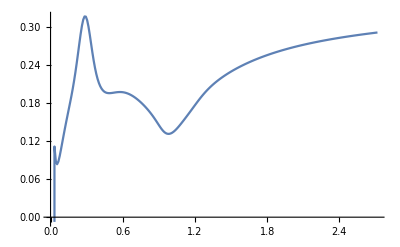

```mathematica
V2p1=Flatten[Import["./PQM2p1flavor/exam/BUFFER/VTOTAL.DAT"]];
T2p1=Flatten[Import["./PQM2p1flavor/exam/BUFFER/T.DAT"]];
mf2p1=Flatten[Import["./PQM2p1flavor/exam/BUFFER/MF.DAT"]];
p2p1=Transpose[{T2p1/TcQM,-(V2p1-V2p1[[1]])/T2p1^4}];
p2p1Tdata=Transpose[{T2p1,-(V2p1-V2p1[[1]])}];
Intp2p1=Interpolation[p2p1Tdata];
dpdT2p1[x_]=D[Intp2p1[x],x];
dpdT22p1[x_]=D[Intp2p1[x],{x,2}];
csNf2p1=Transpose[{T2p1/TcQM,dpdT2p1[T2p1]/(T2p1*dpdT22p1[T2p1])}];
ListLinePlot[csNf2p1]
```

### Lattice

```mathematica
HotQCDp=Flatten[Import["./LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["./LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["./LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["./LQCDdata/hotdpt4u.dat"]];
Tcl=156;
Hotpdown=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["./LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["./LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["./LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT/Tcl,WBp-WBdp}];
WBup=Transpose[{WBT/Tcl,WBp+WBdp}];
WBcs=Table[Import["./LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["./LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT/Tcl,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT/Tcl,WBcs-WBcserr}];
```

## Plot

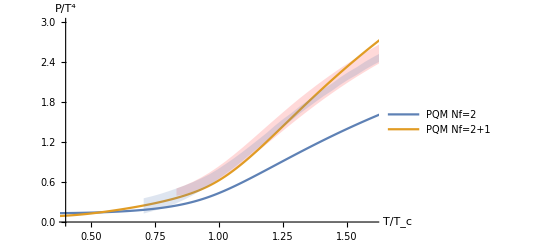

```mathematica
PlotP=Show[ListLinePlot[{p,p2p1,Hotpdown,Hotpup},Filling->{3->{4}},FillingStyle->LightRed,PlotStyle->{Automatic,Automatic,None,None},PlotLegends->{"PQM Nf=2","PQM Nf=2+1"},PlotRange->{{0.4,1.6},{0,3}}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T/T_c","P/T^4"}]
```

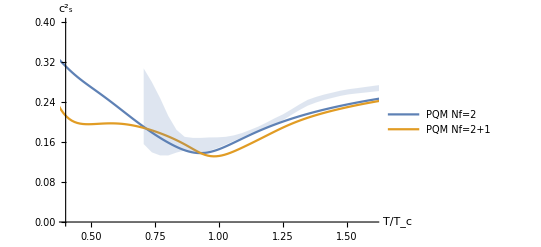

```mathematica
PlotP=Show[ListLinePlot[{csNf2,csNf2p1},FillingStyle->LightRed,PlotStyle->{Automatic,Automatic,None,None},PlotLegends->{"PQM Nf=2","PQM Nf=2+1"},PlotRange->{{0.4,1.6},{0,0.4}}],ListLinePlot[{WBcsdown,WBcsup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T/T_c","(c^2)_s"}]
```

```mathematica
Export["./c2s.pdf",PlotP]
```

./c2s.pdf